# Coherent Photon Background

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Constants

```mathematica
Me=QuantityMagnitude[Quantity["ElectronMass"],"Electronvolts"/"SpeedOfLight"^2];
```

```mathematica
αem=QuantityMagnitude[Quantity["FineStructureConstant"],1];
```

```mathematica
pereV2ToBarn=QuantityMagnitude[Quantity[1,("ReducedPlanckConstant"*"SpeedOfLight"/"Electronvolts")^2],"Barns"];
```

```mathematica
kayserToeV=QuantityMagnitude[Quantity[2*Pi,"ReducedPlanckConstant"*"SpeedOfLight"/"Centimeters"],"Electronvolts"];
```

```mathematica
eVTokg=QuantityMagnitude[Quantity[1,"Electronvolts"/"SpeedOfLight"^2],"Kilograms"];
```

```mathematica
eVToPerYear=QuantityMagnitude[Quantity[1,"Electronvolts"/"ReducedPlanckConstant"],1/"Years"];
```

## Atomic cross section

## Modified form factor

```mathematica
atoms={"Al","As","C","Ga","Ge","N","O","Si"};
```

```mathematica
AtomicData=<|#-><|"Mass"->QuantityMagnitude[ElementData[#,"AtomicMass"],"Electronvolts"/"SpeedOfLight"^2],"Z"->ElementData[#,"AtomicNumber"],"A"->QuantityMagnitude[ElementData[#,"AtomicMass"]]|>&/@atoms|>;
```

```mathematica
KShellEnergy=<|"Al"->-1553.2452,"As"->-11794.841199999999,"C"->-285.878848,"Ga"->-10293.346800000001,"Ge"->-11030.300099999999,"N"->-397.031513,"O"->-526.806013,"Si"->-1833.944|>;
```

```mathematica
KShellMFF[symb_,k_]:=Block[{Z=AtomicData[symb]["Z"],ϵ=1+KShellEnergy[symb]/Me,γ,R,Q},γ=Sqrt[1-(αem*Z)^2];R=2*(Z*αem)^2/ϵ;Q=k/2/Z/αem/Me;2/ϵ/Q*R^(2*γ)*Im[Exp[R*(1-I*Q)]*Gamma[-2*γ,R*(1-I*Q)]]]
```

```mathematica
MFFInterp=<|#->Interpolation[{#[[1]]*10^3,#[[2]]}&/@DeleteDuplicatesBy[SortBy[Import[StringTemplate["Form_factors/modifiedformfactors/small_q/mff_`1`.csv"][#]]~Join~Import[StringTemplate["Form_factors/modifiedformfactors/large_q/mff_`1`.csv"][#]],#[[1]]&],Round[#[[1]],0.01]&]]&/@atoms|>;
```

```mathematica
ModifiedFormFactor=<|#->Function[k,Piecewise[{{MFFInterp[#][k],k<MFFInterp[#]["Domain"][[1,2]]}},KShellMFF[#,k]]]&/@atoms|>;
```

## Delbrück

```mathematica
DSData=<|"θ"->{10,15,30,45,60,75,90,105,120,135,150,175}/360*2*Pi,"Perpendicular"-><|"Re"-><|"1330keV"->{1.70*^-1,1.42*^-1,8.00*^-2,4.32*^-2,2.40*^-2,8.43*^-3,0,-5.18*^-3,-8.84*^-3,-1.17*^-2,-1.24*^-2,-1.32*^-2},"1700keV"->{2.63*^-1,2.07*^-1,9.85*^-2,4.51*^-2,1.88*^-2,4.37*^-3,-4.01*^-3,-4.01*^-3,-9.00*^-3,-1.23*^-2,-1.56*^-2,-1.60*^-2}|>,"Im"-><|"1330keV"->{5.55*^-3,5.26*^-3,3.93*^-3,2.41*^-3,1.07*^-3,5.30*^-5,-6.80*^-4,-1.17*^-3,-1.50*^-3,-1.71*^-3,-1.84*^-3,-1.94*^-3},"1700keV"->{3.72*^-2,3.30*^-2,1.89*^-2,8.19*^-3,1.87*^-3,-1.64*^-3,-3.56*^-3,-4.63*^-3,-5.23*^-3,-5.56*^-3,-5.75*^-3,-5.87*^-3}|>|>,"Parallel"-><|"Re"-><|"1330keV"->{1.79*^-1,1.55*^-1,9.80*^-2,6.43*^-2,4.50*^-2,3.27*^-2,2.60*^-2,2.10*^-2,1.78*^-2,1.55*^-2,1.44*^-2,1.32*^-2},"1700keV"->{2.84*^-1,2.35*^-1,1.37*^-1,8.50*^-2,5.82*^-2,4.23*^-2,3.27*^-2,2.64*^-2,2.23*^-2,1.96*^-2,1.78*^-2,1.60*^-2}|>,"Im"-><|"1330keV"->{5.61*^-3,5.40*^-3,4.49*^-3,3.43*^-3,2.61*^-3,2.15*^-3,1.89*^-3,1.81*^-3,1.80*^-3,1.85*^-3,1.89*^-3,1.94*^-3},"1700keV"->{3.85*^-2,3.56*^-2,2.56*^-2,1.75*^-2,1.25*^-2,9.67*^-3,8.01*^-3,7.08*^-3,6.52*^-3,6.19*^-3,6.00*^-3,5.87*^-3}|>|>|>;
```

```mathematica
DSInterpolate[Eγ_,λ_,reim_]:=Block[{data=(Eγ*10^-3-1330)/(1700-1330)*(DSData[λ][reim]["1700keV"]-DSData[λ][reim]["1330keV"])+DSData[λ][reim]["1330keV"]},Interpolation[{{0,0}}~Join~({DSData["θ"],data}ᵀ)]]
```

## Nuclear Thomson

```mathematica
NTPerp[symb_]:=-AtomicData[symb]["Z"]^2*Me/AtomicData[symb]["Mass"]
```

## Nuclear resonance

```mathematica
σm2[A_]:=QuantityMagnitude[Quantity[0.00225,"Millibarns"/"Megaelectronvolts"/"ReducedPlanckConstant"^2/"SpeedOfLight"^2],1/"Electronvolts"^3]*A^(5/3)
```

```mathematica
NRPerp[symb_,Eγ_]:=Eγ^2/2/Pi^2/(αem/Me)*σm2[AtomicData[symb]["A"]]
```

## Cross section

```mathematica
dσdΩR[symb_,Eγ_]:=Evaluate[Block[{q=2*Eγ*Sin[#/2],AR,A2},AR=ModifiedFormFactor[symb][q];A2=(AR)^2+((AR)*Cos[#])^2;αem^2/2/Me^2*A2]]&
```

```mathematica
dσdΩN[symb_,Eγ_]:=Evaluate[Block[{q=2*Eγ*Sin[#/2],AN=NTPerp[symb],A2},A2=(AN)^2+((AN)*Cos[#])^2;αem^2/2/Me^2*A2]]&
```

```mathematica
dσdΩD[symb_,Eγ_]:=Evaluate[Block[{q=2*Eγ*Sin[#/2],ANR=NRPerp[symb,Eγ],Z=AtomicData[symb]["Z"],A2},A2=(αem^2*Z^2*DSInterpolate[Eγ,"Perpendicular","Re"][#])^2+(αem^2*Z^2*DSInterpolate[Eγ,"Perpendicular","Im"][#])^2+(αem^2*Z^2*DSInterpolate[Eγ,"Parallel","Re"][#])^2+(αem^2*Z^2*DSInterpolate[Eγ,"Parallel","Im"][#])^2;αem^2/2/Me^2*A2]]&
```

```mathematica
dσdΩNR[symb_,Eγ_]:=Evaluate[Block[{q=2*Eγ*Sin[#/2],ANR=NRPerp[symb,Eγ],A2},A2=(ANR)^2+((ANR)*Cos[#])^2;αem^2/2/Me^2*A2]]&
```

```mathematica
dσdΩ[symb_,Eγ_]:=Evaluate[Block[{q=2*Eγ*Sin[#/2],AR,AN=NTPerp[symb],ANR=NRPerp[symb,Eγ],Z=AtomicData[symb]["Z"],A2},AR=ModifiedFormFactor[symb][q];A2=(AR+AN+ANR+αem^2*Z^2*DSInterpolate[Eγ,"Perpendicular","Re"][#])^2+(αem^2*Z^2*DSInterpolate[Eγ,"Perpendicular","Im"][#])^2+((AR+AN+ANR)*Cos[#]+αem^2*Z^2*DSInterpolate[Eγ,"Parallel","Re"][#])^2+(αem^2*Z^2*DSInterpolate[Eγ,"Parallel","Im"][#])^2;αem^2/2/Me^2*A2]]&
```

```mathematica
dσdq[symb_,Eγ_]:=Evaluate[Block[{θ=2*ArcSin[#/2/Eγ],AR=ModifiedFormFactor[symb][#],AN=NTPerp[symb],ANR=NRPerp[symb,Eγ],Z=AtomicData[symb]["Z"],A2},A2=(AR+AN+ANR+αem^2*Z^2*DSInterpolate[Eγ,"Perpendicular","Re"][θ])^2+(αem^2*Z^2*DSInterpolate[Eγ,"Perpendicular","Im"][θ])^2+((AR+AN+ANR)*Cos[θ]+αem^2*Z^2*DSInterpolate[Eγ,"Parallel","Re"][θ])^2+(αem^2*Z^2*DSInterpolate[Eγ,"Parallel","Im"][θ])^2;αem^2*#*Pi/Me^2/Eγ^2*A2]]&
```

## Structure function

## Phonon partial DoS

```mathematica
axisScales=<|"Si"->1,"Ge"->10^-3,"Al2O3"->kayserToeV,"GaAs"->kayserToeV,"SiC"->kayserToeV|>;
```

```mathematica
AtomsPerCell=<|"Al2O3_Al"->2,"Al2O3_O"->3,"GaAs_As"->1,"GaAs_Ga"->1,"Ge"->1,"SiC_C"->1,"SiC_Si"->1,"Si"->1|>;
```

```mathematica
pDoS=<|Block[{data,temp,norm,name=StringDelete[#,{"./Phonon_DOS/","_monoatomic",".csv"}]},data={#[[1]]*axisScales[StringDelete[name[[1]],"_"~~__]],#[[2]]}&/@DeleteDuplicatesBy[Import[#],#[[1]]&]&/@#;temp=Interpolation[#,InterpolationOrder->1]&/@data;norm=Total[(NIntegrate[#[ω],{ω}~Join~#["Domain"][[1]]]&/@temp)*(AtomsPerCell/@name)];AssociationThread[name,Interpolation[{#[[1]],#[[2]]/norm}&/@#,InterpolationOrder->1]&/@data]]&/@GatherBy[FileNames[All,"./Phonon_DOS"],StringDelete[#,{__~~"/","_"~~__}]&]|>;
```

## Debye-Waller factor

```mathematica
DWoverq2ZeroT=<|KeyValueMap[#1->1/4/AtomicData[StringDelete[#1,__~~"_"]]["Mass"]*NIntegrate[#2[ω]/ω,{ω}~Join~#2["Domain"][[1]]]&,pDoS]|>;
```

## Structure function

```mathematica
SFZeroT[target_,n_]:=Evaluate[With[{range=pDoS[target]["Domain"][[1]]},Exp[-2*DWoverq2ZeroT[target]*#1^2]/(n!)*(#1^2/2/AtomicData[StringDelete[target,__~~"_"]]["Mass"])^n*Piecewise[{{If[#2>range[[1]]&&#2<range[[2]],pDoS[target][#2]/#2,0],n==1},{If[#2>2*range[[1]]&&#2<2*range[[2]],NIntegrate[(pDoS[target][ω]/ω)*(pDoS[target][#2-ω]/(#2-ω)),{ω,Max[range[[1]],#2-range[[2]]],Min[range[[2]],#2-range[[1]]]}],0],n==2},{If[#2>3*range[[1]]&&#2<3*range[[2]],NIntegrate[(pDoS[target][ω1]/ω1)*(pDoS[target][ω2]/ω2)*(pDoS[target][#2-ω1-ω2]/(#2-ω1-ω2)),{ω2,Max[range[[1]],#2-2*range[[2]]],Min[range[[2]],#2-2*range[[1]]]},{ω1,Max[range[[1]],#2-range[[2]]-ω2],Min[range[[2]],#2-range[[1]]-ω2]}],0],n==3}}]]]&
```

## Event rate

```mathematica
nγ=QuantityMagnitude[Quantity[1/0.04*4.396833647327371*^-16,"Centimeters"^-3],("Electronvolts"/"SpeedOfLight"/"ReducedPlanckConstant")^3];
```

```mathematica
targets={"Al2O3_Al","Al2O3_O","GaAs_As","GaAs_Ga","Ge","SiC_C","SiC_Si","Si"};
```

```mathematica
CellsPerKg=<|"Al2O3"->1/((2*AtomicData["Al"]["Mass"]+3*AtomicData["O"]["Mass"])*eVTokg),"GaAs"->1/((AtomicData["Ga"]["Mass"]+AtomicData["As"]["Mass"])*eVTokg),"Ge"->1/(AtomicData["Ge"]["Mass"]*eVTokg),"SiC"->1/((AtomicData["Si"]["Mass"]+AtomicData["C"]["Mass"])*eVTokg),"Si"->1/(AtomicData["Si"]["Mass"]*eVTokg)|>;
```

```mathematica
dRdωdqPerKg[target_,Eγ_,n_]:=Evaluate[AtomsPerCell[target]*CellsPerKg[StringDelete[target,"_"~~__]]*nγ*dσdq[StringDelete[target,__~~"_"],Eγ][#1]*SFZeroT[target,n][#1,#2]]&
```

```mathematica
dRdωPerKg[target_,Eγ_,n_,div_]:=Block[{integrand=dRdωdqPerKg[target,Eγ,n],ωfrom=Max[10^-4,n*pDoS[target]["Domain"][[1,1]]*1.01],ωto=n*pDoS[target]["Domain"][[1,2]]*0.99,dω,list},dω=(ωto-ωfrom)/div;list={{0,0}}~Join~ParallelTable[{ω,Quiet[NIntegrate[integrand[q,ω],{q,10^-3/Sqrt[DWoverq2ZeroT[target]],3/Sqrt[DWoverq2ZeroT[target]]}],{NIntegrate::izero,NIntegrate::slwcon,NIntegrate::eincr}]},{ω,ωfrom,ωto,dω}]~Join~{{ωto+dω,0}};With[{interp=Interpolation[list,InterpolationOrder->1]},Piecewise[{{interp[#],#>interp["Domain"][[1,1]]&&#<interp["Domain"][[1,2]]}},0]&]]
```

```mathematica
results=<|Table[target-><|Table[n->dRdωPerKg[target,1461*10^3,n,50],{n,3}]|>,{target,targets}]|>;
```

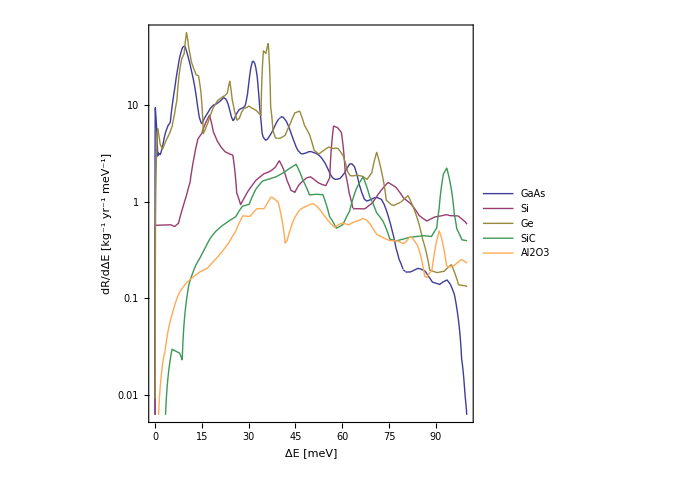

```mathematica
LogPlot[{10^-3*eVToPerYear*Sum[results["GaAs_Ga"][n][ΔE/10^3]+results["GaAs_As"][n][ΔE/10^3],{n,3}],10^-3*eVToPerYear*Sum[results["Si"][n][ΔE/10^3],{n,3}],10^-3*eVToPerYear*Sum[results["Ge"][n][ΔE/10^3],{n,3}],10^-3*eVToPerYear*Sum[results["SiC_Si"][n][ΔE/10^3]+results["SiC_C"][n][ΔE/10^3],{n,3}],10^-3*eVToPerYear*Sum[results["Al2O3_Al"][n][ΔE/10^3]+results["Al2O3_O"][n][ΔE/10^3],{n,3}]},{ΔE,0,100},PlotLegends->Placed[{"GaAs","Si","Ge","SiC","Al2O3"},{Right,Top}],Frame->True,FrameLabel->{"ΔE [meV]","dR/dΔE [kg^-1 yr^-1 meV^-1]"},AspectRatio->1,ImageSize->500,BaseStyle->{FontFamily->"Times"},LabelStyle->21,PlotTheme->"Classic",PlotStyle->{Thick,Thick,Thick,Thick,{Thick,Lighter[Orange]}}]
```